## All Function that are needed

```mathematica
u[x_]:= Sin[2Pi x/6]
k[x_,y_]:=1(*Exp[u[x]-u[y]]*)
listNeighbours[g_,x_,dt_, adj_] := Table[-dt*Part[Part[adj,x],xn](*k[x,xn]*), {xn,Drop[VertexList[NeighborhoodGraph[g,x]],1]}]
```

```mathematica
oneRowOfOnes[m_,n_,i_]:=Module[{res},
res=ConstantArray[0,{m,n}];
res⟦;;,i⟧=1;
res
]
```

```mathematica
ollivierCurvatureMaes[g_,x_,y_,dt_,adj_]:=
Module[{c,m,b},
dx=VertexDegree[g,x];
dy=VertexDegree[g,y]; 
c = {-1+dt*Total[Part[adj,x]]}~Join~listNeighbours[g,x,dt,adj]~Join~{-1+dt*Total[Part[adj,y]]}~Join~listNeighbours[g,y,dt,adj];
(*c={-1+dt*k[x,y],-dt*k[x,y],-dt*k[y,x],-1+ dt*(k[y,x]+k[y,z]),-dt*k[y,z]};*)
m=ArrayFlatten@Table[{oneRowOfOnes[dy+1,dx+1,i],IdentityMatrix[dy+1]},{i,dx+1}];
(*Print[m];*)
b=Flatten@Table[GraphDistance[g,xn,yn],{xn,VertexList[NeighborhoodGraph[g,x]]},{yn,VertexList[NeighborhoodGraph[g,y]]}];
(*b = {0,1,2,1,0,1};*)
(*Print[b];*)
(*(1+(c.LinearProgramming[c,-m,-b])/GraphDistance[g,x,y])*)
-c.LinearProgramming[c,-m,-b,None]]
```

```mathematica
curvature[g_,x_,y_,adj_] := ( -(ollivierCurvatureMaes[g,x,y,0.01,adj] - ollivierCurvatureMaes[g,x,y,0,adj])/(0.01 * GraphDistance[g,x,y]))
```

## Graphs

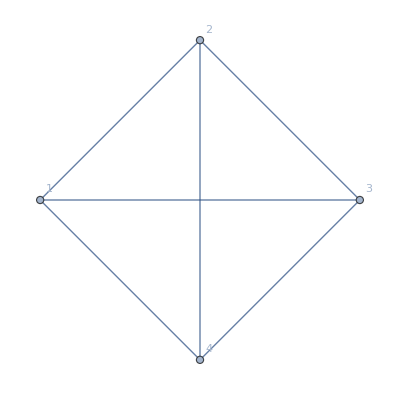

{{0,1,1,1},{1,0,1,1},{1,1,0,1},{1,1,1,0}}

```mathematica
gt = Graph[{1<->2,2<->3,3<->4,4<->1, 1<->3, 2<->4}, VertexLabels->Automatic]
adjgt = Normal[AdjacencyMatrix[gt]]
```

```mathematica
curvature[gt, 4,1,adjgt]
```

4.

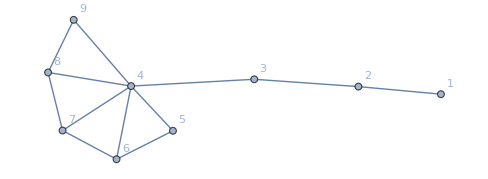

{{0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0},{0,0,1,0,1,1,1,1,1},{0,0,0,1,0,0,1,0,0},{0,0,0,1,0,0,1,1,0},{0,0,0,1,1,1,0,0,0},{0,0,0,1,0,1,0,0,1},{0,0,0,1,0,0,0,1,0}}

```mathematica
gtest = Graph[{1<->2,2<->3,3<->4,4<->5,4<->7,5<->6,6<->7, 7<->8, 4<->9, 8<->9,4<->6,4<->8}, VertexLabels->Automatic]
adjgtest = Normal[AdjacencyMatrix[gtest]]
```

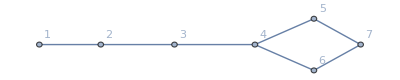

{{0,1,0,0,0,0,0},{1,0,1,0,0,0,0},{0,1,0,1,0,0,0},{0,0,1,0,1,1,0},{0,0,0,1,0,0,1},{0,0,0,1,0,0,1},{0,0,0,0,1,1,0}}

linetree.pdf

```mathematica
gtest2 = Graph[{1<->2,2<->3,3<->4,4<->5,4<->6,5<->7,6<->7}, VertexLabels->Automatic]
adjgtest2 = Normal[AdjacencyMatrix[gtest2]]
```

```mathematica
curvature[gtest2,5,7, adjgtest2]
```

2.

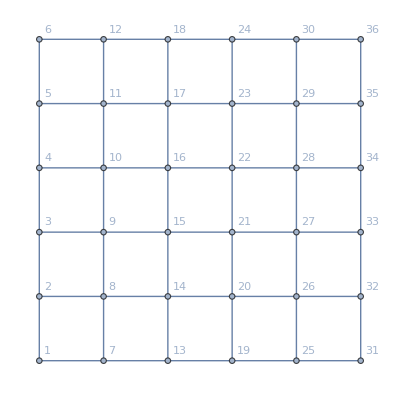

```mathematica
g= GridGraph[{6,6}  , VertexLabels->Automatic]
```

```mathematica
adj = Normal[AdjacencyMatrix[g]]
```

{{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0}}

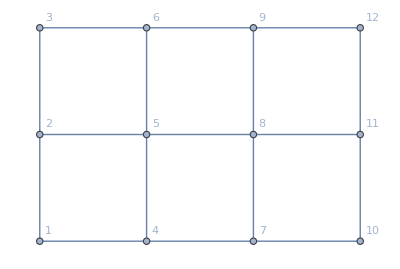

{{0,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0},{0,1,0,1,0,1,0,1,0,0,0,0},{0,0,1,0,1,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0,1,0,1,0},{0,0,0,0,0,1,0,1,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,1,0,1},{0,0,0,0,0,0,0,0,1,0,1,0}}

```mathematica
g2 = GridGraph[{3,4}, VertexLabels->Automatic]
adjacency = Normal[AdjacencyMatrix[g2]]
```

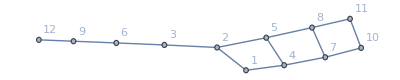

```mathematica
g3 = AdjacencyGraph[{{0,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}, VertexLabels->Automatic]
```

```mathematica
adj = Normal[AdjacencyMatrix[g3]]
```

{{0,1,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,1,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,1,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0},{0,0,0,1,0,0,0,1,0,1,0,0},{0,0,0,0,1,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0,0,1},{0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}

## Curvature

```mathematica
step=1;
Do[Print["edge ","(",i,",",i+step,")",": ",curvature[g3,i,i+step,adj]],{i,1,Length[Part[adj,1]]-step}]
```

edge (1,2): 1.

edge (2,3): -1.

edge (3,4): 0.333333

edge (4,5): 2.

edge (5,6): -0.333333

edge (6,7): 0.2

edge (7,8): 2.

edge (8,9): -0.2

edge (9,10): 0.285714

edge (10,11): 2.

edge (11,12): 0.142857

```mathematica
curvature[g3,8,5, adj]
```

0.

```mathematica
curvature[g,4,7,adj]
```

0.

```mathematica
curvature[g3, 2,5,adj]
```

0.

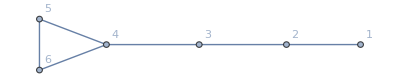

{{0,1,0,0,0,0},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,1},{0,0,0,1,0,1},{0,0,0,1,1,0}}

```mathematica
h = Graph[{1<->2, 2<->3,3<->4, 4<->5, 4<->6, 5<->6}];Graph[h,VertexLabels->Automatic]
adjh = Normal[AdjacencyMatrix[h]]
```

```mathematica
step=1;
Do[Print["edge ","(",i,",",i+step,")",": ",curvature[h,i,i+step,adjh]],{i,1,Length[Part[adjh,1]]-step}]
```

edge (1,2): 1.

edge (2,3): 0.

edge (3,4): -1.

edge (4,5): 2.

edge (5,6): 3.

```mathematica
curvature[h,5,7,adjh]
```

2.

```mathematica
curvature[h,4,6,adjh]
```

2.

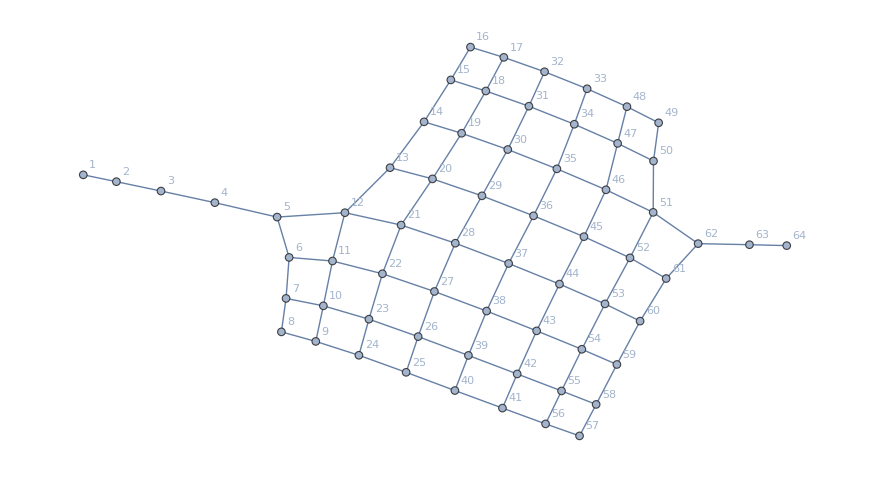

```mathematica
test = AdjacencyGraph[{{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}}, VertexLabels->Automatic]
```

```mathematica
adjtest = {{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}};
```

```mathematica
curvature[test,28,37,adjtest]
```

0.

## Curvature from file

```mathematica
filelist = Table["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_"<>ToString[i]<>".txt", {i,21,40}]
```

{/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_21.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_22.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_23.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_24.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_25.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_26.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_27.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_28.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_29.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_30.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_31.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_32.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_33.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_34.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_35.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_36.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_37.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_38.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_39.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_40.txt}

```mathematica
filelist2 = Table["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_"<>ToString[i]<>".txt", {i,21,40}]
```

{/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_21.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_22.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_23.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_24.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_25.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_26.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_27.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_28.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_29.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_30.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_31.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_32.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_33.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_34.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_35.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_36.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_37.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_38.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_39.txt,/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_curvature_flatnobc_40.txt}

```mathematica
Do[data = OpenRead[Part[filelist,j]];
curvbegin = {};
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvbegin, curvature[AdjacencyGraph[temp], 5,6, temp]]];
WriteLine[ToString[Part[filelist2,j]], List[curvbegin]];
curvmid = {};
data = OpenRead[Part[filelist,j]];
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvmid,curvature[AdjacencyGraph[temp], 25,26, temp]]];
WriteLine[ToString[Part[filelist2,j]], List[curvmid]];
curvend = {};
data = OpenRead[Part[filelist,j]];
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvend, curvature[AdjacencyGraph[temp], 45,46, temp]]];
WriteLine[ToString[Part[filelist2,j]], List[curvend]];
Print[j-1], {j,1,20}]
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

### manually

```mathematica
data = OpenRead["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/adjacency_flatnobc_0.txt"];
```

```mathematica
curvbegin = {};
```

```mathematica
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvbegin, curvature[AdjacencyGraph[temp], 5,6, temp]]]
```

```mathematica
curvbegin
```

{0.,0.,0.,0.,-1.,0.,0.,0.,1.,0.,0.,0.,-1.,-1.,0.,0.,2.,1.,1.,1.,1.,-1.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,-1.,0.,1.,0.,-1.,0.,2.,0.,1.,0.,1.,0.,0.,-1.,2.,0.,0.,0.,1.,0.,0.,2.,2.,0.,-1.,0.,0.,0.,2.,1.,0.,0.,1.,-1.,0.,2.,0.,0.,-1.,0.,2.,-1.,1.,0.,-1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.}

```mathematica
WriteLine["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_flat_nobc/curvature_flatnobc_0.txt", List[curvbegin]]
```

```mathematica
curvmid = {};
```

```mathematica
data = OpenRead["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_flat_nobc/adjacency_flatnobc_0.txt"];
```

```mathematica
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvmid,curvature[AdjacencyGraph[temp], 25,26, temp]]]
```

```mathematica
curvmid
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,1.,0.,0.,0.,0.,0.,-1.,2.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,2.,2.,1.,0.,0.,0.,1.,0.,0.,1.,0.,1.,2.,2.,-1.,0.,0.,1.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,1.,1.,1.,1.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,1.,2.,0.,0.,0.,0.}

```mathematica
WriteLine["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_flat_nobc/curvature_flatnobc_0.txt", List[curvmid]]
```

```mathematica
curvend = {};
```

```mathematica
data = OpenRead["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_flat_nobc/adjacency_flatnobc_0.txt"];
```

```mathematica
For[i=1,i<= 101, i++, temp = Read[data]; AppendTo[curvend, curvature[AdjacencyGraph[temp], 45,46, temp]]]
```

```mathematica
curvend
```

{0.,0.,0.,0.,-1.,0.,-1.,0.,0.,0.,0.,-1.,0.,0.,-1.,0.,1.,-2.,0.,0.,-1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,2.,2.,0.,1.,1.,1.,0.,0.,2.,1.,2.,2.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,-1.,1.,0.,0.,0.,0.,0.,0.,2.,1.,0.,2.,-1.,0.,1.,2.,0.,0.,-1.,0.,1.,0.,0.,0.,0.,0.,0.,0.,-1.,0.,0.,0.,1.,-1.,0.,0.,0.,2.,-1.,0.,1.}

```mathematica
WriteLine["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_flat_nobc/curvature_flatnobc_0.txt", List[curvend]]
```

## Test for graph

```mathematica
data = OpenRead["/home/sander/Documents/School/univ/Fysica/master/fase_3/thesis/notes/data_lowT/data_flat_nobc/lowT_adjacency_flatnobc_0.txt"];
```

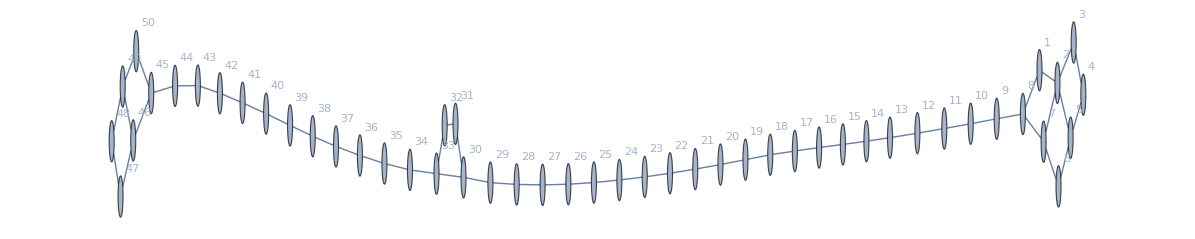

```mathematica
gtest = AdjacencyGraph[Read[data], VertexLabels->Automatic]
```

```mathematica
curvature[gtest,25,26, Read[data]]
```

1.